# HW 1 - ASTR404

## Daniel George - dgeorge5@illinois.edu

## Q3) Binary star data

## Importing data in solar units

```mathematica
tSun=QuantityMagnitude@Entity["Star","Sun"]["EffectiveTemperature"];SetDirectory["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR404\\"];
dataS=SemanticImport["eker_2014_simple.dat"][All,{"T1"->(#/tSun&),"T2"->(#/tSun&)}];
```

## a) & b) Radius and temperature vs mass

### Scatter plots and best fits

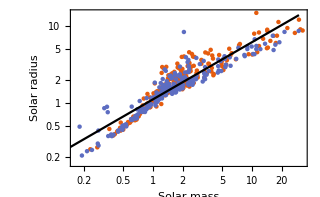
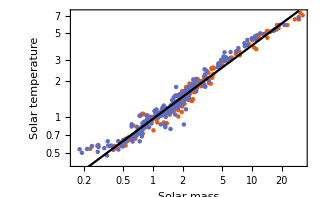

```mathematica
SetOptions[ListLogLogPlot,PlotStyle->PointSize[.01],PlotTheme->"Scientific",Frame->True,PlotRange->All];
fit[s_]:=LinearModelFit[Sort[Join@@(Log10@Values@Normal@dataS[All,#]&/@{{"M1",s<>"1"},{"M2",s<>"2"}})],{1,x},x];
Show[ListLogLogPlot[Values@Normal@dataS[All,#]&/@{{"M1",#1<>"1"},{"M2",#1<>"2"}},FrameLabel->{"Solar mass",#2},ImageSize->320],LogLogPlot[10^fit[#1][Log10[M]],{M,0,30},PlotStyle->Black]]&@@@{{"R","Solar radius"},{"T","Solar temperature"}}//Row
```

We can see that both the radius and the temperature increase monotonically with increase in mass of the stars. Moreover, they seem to fit a power law relationship since a linear fit to the log-log plot matches closely.

There is a larger spread in the radius when mass increases whereas temperature appears to converge to the fit with increasing mass.

### Fitting functions in solar units

```mathematica
#==10^fit[#][Log10@M]&/@{"R","T"}//Column
```

R==1.12229 M^0.736893
T==0.967053 M^0.61208

## c) Luminosity vs mass

### Scatter plot along with best fit

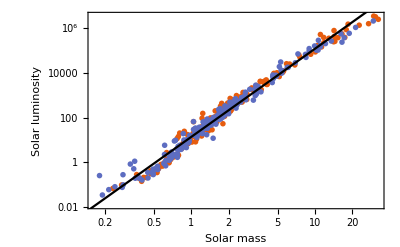

```mathematica
dataL=Transpose[{Normal@dataS[All,"M"<>#],Normal@dataS[#^4&,"T"<>#]*Normal@dataS[4Pi#^2&,"R"<>#]}]&/@{"1","2"};
fitL=LinearModelFit[Join@@Log10@dataL,{1,x},x];
Show[ListLogLogPlot[dataL,FrameLabel->{"Solar mass","Solar luminosity"}],
LogLogPlot[10^fitL[Log10@M],{M,0,30},PlotStyle->Black]]
```

We can see that the luminosity also increases monotonically with increase in mass of the stars. Moreover, the luminosity appears to fit a power law relationship with mass since the linear fit to the log-log plot matches closely. The spread of the points appear to be higher for low and high masses.

### Fitting function in solar units

```mathematica
"L"==10^fitL[Log10[M]]
```

L==13.8428 M^3.92211

## Q2) Properties of Deneb

### Defining parameters of Deneb

```mathematica
Rs=Quantity[7.72 10^10,"Meter"];
Ts=Quantity[8525.,"Kelvin"];
ds=Quantity[440.,"Parsecs"];
```

## a) Luminosity

L==4 π R^2 σ T^4

### SI units

```mathematica
Ls=UnitConvert[4Pi Rs^2 Quantity[, "StefanBoltzmannConstant"]Ts^4,"SI"]
```

2.24302×10^31 W

### Solar units

```mathematica
UnitConvert[Ls,"SolarLuminosity"]
```

58610.9 L_☉

## b) Parallax and distance modulus

### Parallax

Parallax = Diameter (in AU)/Distance (in Parsecs)

```mathematica
Quantity[QuantityMagnitude[2Rs,"AU"]/QuantityMagnitude[ds,"Parsecs"],"ArcSeconds"]
```

0.00234568 "

### Distance modulus

μ==5 log_10(d in parsecs)-5

```mathematica
5Log10[QuantityMagnitude[ds,"Parsecs"]]-5
```

8.21726

## c) Radiant flux at star’s surface

Flux is luminosity divided by surface area of star:

```mathematica
UnitConvert[Ls/(4Pi Rs^2),"SI"]
```

2.99494×10^8 N/(m s)

## d) Radiant flux at earth’s surface

Luminosity divided by area of sphere with radius equal to distance to earth:

```mathematica
UnitConvert[Ls/(4Pi ds^2),"SI"]
```

9.68315×10^-9 N/(m s)

## e) Peak wavelength

### Looking up Wien’s displacement law

```mathematica
eqW=FormulaData[{"WienDisplacementLaw", "Wavelength"}]
```

λ_max Wavelength==(1 b)/(T Temperature)

### Substituting value of temperature

```mathematica
eqW[[1]]==UnitConvert[eqW[[2]]/."T" "Temperature"->Ts,"meters"]
```

λ_max Wavelength==3.39915×10^-7 m

## Q1) Planck’s law limits

## a) Rayleigh-Jeans law

### Defining Planck function

```mathematica
Bv=2 h c^2 /(Exp[h c /k /T/λ]-1)/λ^5
```

(2 c^2 h)/((-1+ⅇ^((c h)/(k T λ))) λ^5)

### Taylor expansion for λ^-1

```mathematica
TE1=Normal@Series[Bv/. λ->1/x,{x,0,10}]/.x->1/λ
```

(c^7 h^6)/(15120 k^5 T^5 λ^10)-(c^5 h^4)/(360 k^3 T^3 λ^8)+(c^3 h^2)/(6 k T λ^6)-(c^2 h)/λ^5+(2 c k T)/λ^4

### Substituting λ = n*h*c/(k*T)

```mathematica
TE1/.λ->n*h*c/(k*T)
```

(k^5 T^5)/(15120 c^3 h^4 n^10)-(k^5 T^5)/(360 c^3 h^4 n^8)+(k^5 T^5)/(6 c^3 h^4 n^6)-(k^5 T^5)/(c^3 h^4 n^5)+(2 k^5 T^5)/(c^3 h^4 n^4)

Therefore for n >> 1, we can approximate the equation using just the last term which corresponds to the following term in the Taylor series:

(2 c k T)/λ^4

## b) Wien’s function

### Substituting λ = n*h*c/(k*T)

```mathematica
Bv/.λ->n*h*c/(k*T)
```

(2 k^5 T^5)/(c^3 (-1+ⅇ^(1/n)) h^4 n^5)

### Taking limit

In the limit n << 1, e^(1/n) - 1 ~ e^(1/n). Therefore we can ignore the 1 in the denominator. This gives:

(2 c^2 ⅇ^(-(c h)/(k T λ)) h)/λ^5

Therefore the constants are:

a==2 c^2 h
b==(c h)/k